```mathematica
Needs["HierarchicalClustering`"]
data =Import["C:\\Users\\Student\\Desktop\\Модели_и_методы\\shoes_normed.csv"]

hierarcgdata =Agglomerate[data,Linkage->"Complete", DistanceFunction->ManhattanDistance]
```

{{0,1,0,1,0,1,0,1,0,0,1,0,1,1,1,1,1,0,0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,0,1,1,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,1,0,0,1,0,0,0,0,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,0,1,1,0,0,0,1,1,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0},{1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,1,1,1,0,1,0,0,1,1,0,1,1,0,1,1,0,1,0,1,1,0,0,0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1},{1,0,0,0,1,0,1,1,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,0,1,1,1,0,1,0,0,0,1,1,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,1,0,1,1,1,0,1,1,0,1,1,1,1,0,1,0,1,1,0,1,0,1,1,0,1,1,1,1,0,1,0,0,1,0,1,1,1,1,1,1,1,1,1,0,0,1,1,0,0,0,1,1,1,0,0,1,1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,0,1},{1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,1,1,0,0,0,1,1,0,0,1,0,1,0,1,0,1,0,1,0,0,0,1,1,1,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,1,1,1,0,1,1,0,0,1,1,1,1,1,0,1,0,1,1,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,1,1,1,0,1,1,1,1,0,1,1,1,0,1,0,0,1,0,1,0,1,1,1,1,0,1,0,1,0,1,1,1,1,0,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,0},{1,0,1,0,0,0,0,0,1,1,0,0,0,0,1,1,0,1,1,1,1,0,0,0,1,1,0,1,0,0,1,1,1,1,1,1,1,1,0,0,1,1,0,1,0,0,1,0,0,0,1,0,0,1,1,1,0,0,0,1,1,0,1,1,0,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{1,1,0,0,1,0,1,1,1,0,1,1,0,0,1,1,1,0,0,1,0,0,0,1,0,0,1,0,1,1,0,1,1,0,1,1,1,1,0,1,1,0,1,1,0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,1,1,1,0,0,0,0,1,0,1,1,0,1,1,1,1,1,1,1,1,1},{1,0,1,0,1,1,0,1,0,1,0,1,0,1,1,0,1,1,0,0,0,0,0,1,0,1,1,0,0,1,0,0,0,1,1,1,0,0,0,1,1,0,1,0,0,1,1,1,0,0,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,0,1,1,1,0,0,1,0,1,1,0,1,0,1,1},{0,0,0,0,1,1,0,0,0,0,1,0,0,1,0,0,1,1,1,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,1,1,0,1,0,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,1,1,0,0,1,0,1}}

Agglomerate::ties: 3 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[{0,1,0,1,0,1,0,1,0,0,1,0,1,1,1,1,1,0,0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,0,1,1,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1},{0,0,0,0,1,1,0,0,0,0,1,0,0,1,0,0,1,1,1,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,1,1,0,1,0,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,1,1,0,0,1,0,1},35,1,1],Cluster[Cluster[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,0},{1,1,0,0,1,0,1,1,1,0,1,1,0,0,1,1,1,0,0,1,0,0,0,1,0,0,1,0,1,1,0,1,1,0,1,1,1,1,0,1,1,0,1,1,0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,1,1,1,0,0,0,0,1,0,1,1,0,1,1,1,1,1,1,1,1,1},34,1,1],Cluster[Cluster[Cluster[{1,1,1,1,1,0,0,0,0,1,1,1,0,1,0,0,1,1,0,1,1,0,1,1,0,1,0,1,1,0,0,0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1},{1,1,1,1,1,1,0,0,0,1,1,1,0,1,1,0,0,1,1,1,1,1,0,1,0,1,1,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,1,1,1,0,1,1,1,1,0,1,1,1,0,1,0,0,1,0,1,0,1,1,1,1,0,1,0,1,0,1,1,1,1,0,1,0},22,1,1],{1,0,1,0,1,1,0,1,0,1,0,1,0,1,1,0,1,1,0,0,0,0,0,1,0,1,1,0,0,1,0,0,0,1,1,1,0,0,0,1,1,0,1,0,0,1,1,1,0,0,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,0,1,1,1,0,0,1,0,1,1,0,1,0,1,1},30,2,1],{1,1,1,1,1,1,0,1,0,1,1,1,0,1,1,0,1,1,1,1,0,1,0,1,1,0,1,0,1,1,0,1,1,1,1,0,1,0,0,1,0,1,1,1,1,1,1,1,1,1,0,0,1,1,0,0,0,1,1,1,0,0,1,1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,0,1},35,3,1],39,2,4],53,2,6],Cluster[Cluster[{0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,1,0,0,1,0,0,0,0,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,0,1,1,0,0,0,1,1,0,0},Cluster[Cluster[{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0},{1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},18,1,1],Cluster[Cluster[Cluster[{1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0},Cluster[Cluster[{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0},Cluster[Cluster[{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},Cluster[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},3,1,1],6,1,2],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1},8,3,1],10,1,4],{0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},13,5,1],15,1,6],{0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},18,7,1],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},19,8,1],29,2,9],41,1,11],Cluster[{1,0,1,0,0,0,0,0,1,1,0,0,0,0,1,1,0,1,1,1,1,0,0,0,1,1,0,1,0,0,1,1,1,1,1,1,1,1,0,0,1,1,0,1,0,0,1,0,0,0,1,0,0,1,1,1,0,0,0,1,1,0,1,1,0,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1},Cluster[{1,0,0,0,1,0,1,1,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,0,1,1,1,0,1,0,0,0,1,1,0,0},{1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,1,1,0,0,0,1,1,0,0,1,0,1,0,1,0,1,0,1,0,0,0,1,1,1,0},26,1,1],31,1,2],43,12,3],71,8,15]

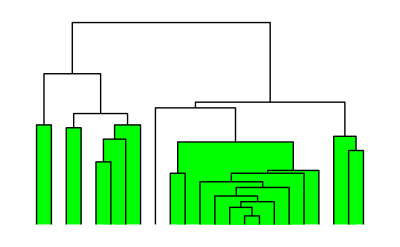

```mathematica
DendrogramPlot[hierarcgdata,HighlightLevel->6]
```